# Hoja de Trabajo 1

Diego Sarceño, 20190019

## Problema 5:

```mathematica
ϕ0 = π^(-1/4)*Exp[-x^2/2]
ϕ1=(4/π)^(1/4)*x*Exp[-x^2/2]
```

(ⅇ^(-x^2/2))/π^(1/4)

(√2 ⅇ^(-x^2/2) x)/π^(1/4)

```mathematica
H[f_]:=-1/2*D[f,{x,2}]+1/2*x^2*f
```

```mathematica
H[ϕ0]//FullSimplify
```

(ⅇ^(-x^2/2))/(2 π^(1/4))

```mathematica
H[ϕ1]//FullSimplify
```

(3 ⅇ^(-x^2/2) x)/(√2 π^(1/4))

Ahora, tomando ϕ_2(x)

```mathematica
ϕ2=(4*π)^(-1/4)*(a*x^2-1)*Exp[-x^2/2]
```

(ⅇ^(-x^2/2) (-1+a x^2))/(√2 π^(1/4))

```mathematica
Integrate[ϕ0*ϕ2,{x,-∞,∞}]
```

(-2+a)/(2 √2)

```mathematica
Integrate[ϕ1*ϕ2,{x,-∞,∞}]
```

0

```mathematica
a=2
```

2

```mathematica
a=2
```

2

```mathematica
H[ϕ2]//FullSimplify
```

(5 ⅇ^(-x^2/2) (-1+2 x^2))/(2 √2 π^(1/4))

## Problema 6:

Definimos las constantes a utilizar:

```mathematica
ℏ=1.054*10^-34
```

1.054×10^-34

```mathematica
m=9.11*10^-31
```

9.11×10^-31

```mathematica
w=5*10^-6
```

1/200000

Función a graficar.

```mathematica
(* En términos de los polinomios de Hermite *)
```

```mathematica
ψ[x_,n_]:=1/(√(2^n*Factorial[n]))*((m*w)/(ℏ*π))^(1/4)*Exp[-(m*w*x^2)/(2*ℏ)]*HermiteH[n,√((m*w)/ℏ)*x]
```

```mathematica
(* Lista de funciones a plotear.b4 *)
func=ψ[x,#]&/@Range[0,2]
```

{0.342472 ⅇ^(-0.0216082 x^2),0.100685 ⅇ^(-0.0216082 x^2) x,0.121082 ⅇ^(-0.0216082 x^2) (-2.+0.172865 x^2)}

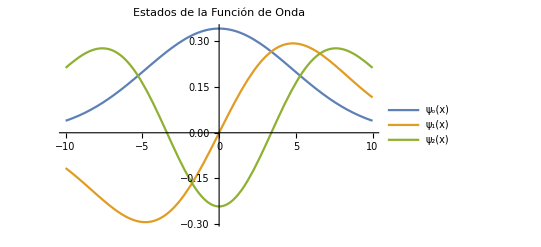

```mathematica
Plot[func,{x,-10,10},PlotLegends->{"ψ_o(x)","ψ_1(x)","ψ_2(x)"},PlotLabel->"Estados de la Función de Onda"]
```

c)

```mathematica
Integrate[func[[1]]*func[[2]],{x,-∞,∞}]
Integrate[func[[1]]*func[[3]],{x,-∞,∞}]
Integrate[func[[2]]*func[[3]],{x,-∞,∞}]
```

0.

2.22045×10^-16

0.